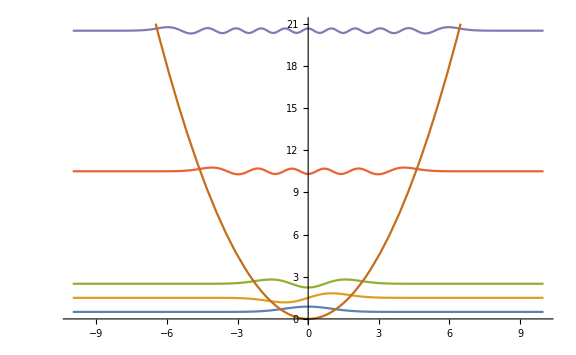

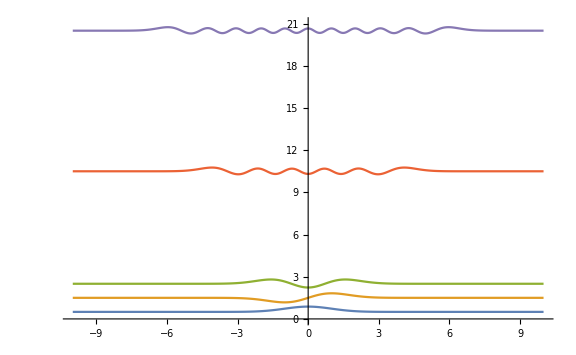

```mathematica
Energy[n_]:=(2 n+1)× ℏ/2 ×ω;

ψ[z_,n_]:=1/2 1/Sqrt[2^n n!]×((m ω)/(π ℏ))^(1/4)×Exp[-((m ω z^2)/(2 ℏ))]× HermiteH[n,Sqrt[(m ω)/ℏ] z];
φ[p_, n_]:=FourierTransform[1/2 1/Sqrt[2^n n!]×((m ω)/(π ℏ))^(1/4)×Exp[-((m ω z^2)/(2 ℏ))]× HermiteH[n,Sqrt[(m ω)/ℏ] z], z, p];

m=1;
ω=1;
ℏ=UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"];
ℏ=QuantityMagnitude[ℏ];
ℏ=1;

Plot[{Evaluate@Table[Energy[n]+ψ[z,n],{n,{0,1, 2, 10, 20}}],z^2/2},{z,-10,10},PlotRange->{0,21}, ImageSize->Large]
Plot[{Evaluate@Table[Energy[n]+ψ[p, n],{n,{0,1, 2, 10, 20}}]},{p,-10,10},PlotRange->{0,21}, ImageSize->Large]
```

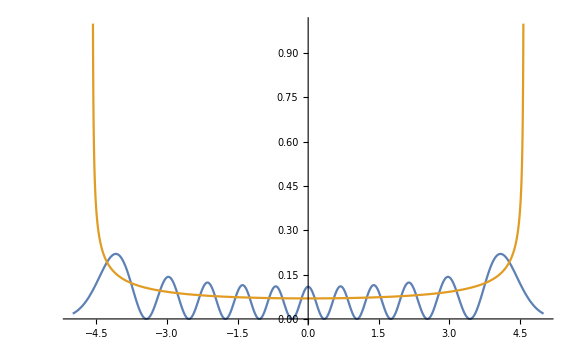

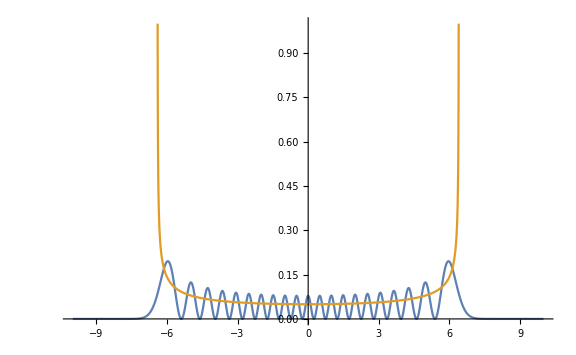

```mathematica
P[z_, n_] := (ω/π)×Sqrt[m/(2Energy[n]- z^2)]
Plot[{Evaluate[π ψ[z,10]^2],Evaluate[P[z,10]]},{z,-5,5},PlotRange->{0,1}, ImageSize->Large]
Plot[{Evaluate[π  ψ[z,20]^2],Evaluate[P[z,20]]},{z,-10,10},PlotRange->{0,1}, ImageSize->Large]
```

```mathematica
A[x_,y_, n1_, n2_] := 2/L × Sin[n1 π x/L1] Sin[n2 π y/L2];
L1 =1;
L2 = 2;
Plot3D[Evaluate[A[x,y,1, 4]],{x,0,1},{y,0,2}, PlotStyle->{Orange,Specularity[White,10]}]
```

-Graphics3D-

```mathematica
B[ρ_, θ_, m_] := BesselJ[m,ρ] Cos[m×θ];
m =5;
k = 1;
ParametricPlot3D[{2 B[ρ, θ, m], ρ Cos[θ], ρ Sin[θ]}, {ρ, 0, BesselJZero[m,k]}, {θ, 0, 2 π},  PlotStyle->{Orange,Specularity[White,10]}]
```

-Graphics3D-